# The Isomorphism of 3-Qubit Hadamards and E_8

J Gregory Moxness

CC BY - NC - SA 4.0 DEED/Attribution-NonCommercial-ShareAlike 4.0 International

www.TheoryOfEverything . org

This paper presents several notable properties of the matrix 𝕌 shown to be related to the isomorphism between $H_4$ and $E_8$. The most significant of these properties is that 𝕌.𝕌 is to rank 8 matrices what the golden ratio is to numbers. That is to say, the difference between it and its inverse is the identity element, albeit with a twist. Specifically, 𝕌.𝕌-(𝕌.𝕌)^-1 is the reverse identity matrix or standard involutory permutation matrix of rank 8. It has the same palindromic characteristic polynomial coefficients as the normalized 3-qubit Hadamard matrix with 8-bit binary basis states, which is known to be isomorphic to E8 through its (8,4) Hamming code.

## Initializations (snippets)

### General Global Initialization

Standard & Others’ Packages

```mathematica
(* Define conditionally applied doPrint, doQuiet and doOff processing *)
print:=If[doPrint,Print@##]&;

quiet[in_]:=If[doQuiet,Quiet[in],in];
Attributes[quiet]={HoldAll};

off[sym_]:=(
print["doOff=",doOff," off=",sym];
If[doOff,Off@sym]);
```

```mathematica
<< MultivariateStatistics`; 
<< ComputationalGeometry`;
```

```mathematica
(**)
If[doSuperLie,<<Quaternions`];
```

```mathematica
Off[General::munfl];
```

```mathematica
<<NDSolve`FEM`
```

```mathematica
(* Tetrahedral Mesh Generator package *)
<<TetGenLink`
```

```mathematica
Off[Set::shape];
```

```mathematica
Off[TetGenConvexHull::tetfc];
```

```mathematica
Off[Volume::nmet];
```

```mathematica
off[Volume::reg];
```

```mathematica
off[RegionCentroid::reg];
```

```mathematica
off[ViewPoint::nlist3];
```

```mathematica
Off[Export::autofix];
```

```mathematica
Off[General::stop];
```

```mathematica
Off[AffineTransform::inpf];
```

```mathematica
Off[BinaryWrite::nocoerce];
```

```mathematica
Off[XMLElement::attrhs];
```

```mathematica
off[HighlightMesh::meshreg];
```

```mathematica
Off[PropertyValue::pvobj];
(**)
```

```mathematica
off[ConvexHullMesh::affind]
```

```mathematica
off[ConvexHullMesh::pts]
```

```mathematica
Off[Show::gtype]
Off[Show::gcomb]
Off[Show::shx]
```

```mathematica
Off[TetGenTetrahedralize::reterr]
```

```mathematica
Off[TetGenDelaunay::tetgpts]
```

This is for either LieART or GroupMath.
Caution : It uses names that can step on my functions unless modified e.g. {An, Bn, Cn, Dn, E(4,5,6,7,8),F4,G2}

```mathematica
(* SuperLie Algebra **)
If[doSuperLie&&working,
off[Solve::svars];
off[ToExpression::sntx]]
(* This is a replacement rule that corrects my code that uses undefined symbols (which SuperLie replaces) *)
slRep:=If[doSuperLie,ToExpression@"{Global`GPlus→Global`Plus,Global`GTimes→Global`Times,Global`GPower→Global`Power,GPlus→Plus,GTimes→Times,GPower→Power}",xxx->1];
```

Off::mgre: Message group Equations may not give solutions for all "solve" variables. was not resolved to a list of messages of the form symbol::name or symbol::name::language.

```mathematica
(* LieART **)
If[doLieART&&working,
<<LieART`];
```

```mathematica
(* GroupTheory **)
If[doGroupTheory&&working,
off[Transpose::nmtx];
<<GroupTheory`];

If[doGroupTheory,
Unprotect[ex,a,b,c,d,F4]];
```

```mathematica
(* GroupMath **)
If[working&&doGroupMath,
(*)Unprotect@C;**)
Unprotect@BlockDiagonalMatrix;
(*)Clear[a,d,f,(* group names *)
e6,e7,e8,so10,so11,so12,so13,so14,so15,so16,so17,so3,so5,so6,so7,so8,so9,su2,su3,su4,su5,su6,su7,su8,u1];**)
<<GroupMath`;(*)
<<Sym2Int`**)];
```

paclet:GroupMath/tutorial/GroupMathDoc | XXXXXXXXXXXXXXXXXXXXXXXXXXX GroupMath XXXXXXXXXXXXXXXXXXXXXXXXXXVersion: 1.1.2 (6/May/2020)Author: Renato FonsecaReference: 2011.01764 [hep-th]Website: http://renatofonseca.net/groupmathBuilt-in documentation: paclet:GroupMath/tutorial/GroupMathDocXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX

Global

```mathematica
first=If[Length@#==0||#==={{}},#,First@Flatten@#]&;
position[x_,y_]:=first@Position[x,y,1,Heads->False];
```

```mathematica
(* The symbol φ is the main reference for resolving the Golden Ratios. 
It is only evaluated to a symbolic or numeric value using φRep replacement rules *)
Clear[ϕ,σ,Φ,τ,φ];
(* Upper (and lower) case Phi(Φ=(1+√5)/2) (and phi ϕ=(1-√5)/2)) represent large (and small) Golden Ratio (respectively) *)
ϕ=1/φ;
(* σ & τ are Galois conjugates, this will get stepped on from the CKM UI *)
σ=-1/φ/.slRep;
τ=Φ=φ;

(* 𝕌Det1f is a scale factor to make Det@𝕌=1 *)𝕌Det1f=2 √ϕ /.slRep;
```

```mathematica
(* Create assumptions and replacement rules for φ and ω for automated symbolics *)
φAssumptions:={φ∈Reals,φ^(1/2)∈Reals,φ^(3/2)∈Reals,N[(√5+1)/2]≥φ>N[(√5+1)/2]-chop^2(*),ω∈Complexes**)};
φRep:={φ->(√5+1)/2,ω->ⅇ^(ⅈ 2π/3)};
```

```mathematica
(* GroupMath steps on CircleTimes *)
If[working&&!doGroupMath,
CircleTimes[a_,b_]:=KroneckerProduct[a,b]];

KroneckerSum[a_,b_]/;MatrixQ[a]&&MatrixQ[b]:=Catch@
Module[{n,p,m,q},
{n,p}=Dimensions[a];
{m,q}=Dimensions[b];
If[n≠p||m≠q,Throw[Failed]];
KroneckerProduct[a,IM@m]+
KroneckerProduct[IM@n,b]];

fb:=Fibonacci;

σP@i_:=PauliMatrix@i;
MatrixForm[σP@#⊗IdentityMatrix@#]&/@Range@3
```

{(0 | 1
1 | 0)⊗(1),(0 | -ⅈ
ⅈ | 0)⊗(1 | 0
0 | 1),(1 | 0
0 | -1)⊗(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)}

```mathematica
(* Tetration as ^n a := a^(a^(a^(...n))) *)
tetration[a_?NumericQ,0]:=1;
tetration[a_?NumericQ,n_]:=a^(Sign@n tetration[a,n-Sign@n]);
tetration[a_?ListQ,n_]:=MatrixPower[a,n];
MakeExpression[RowBox[{SuperscriptBox["",n_],a_}],StandardForm]:=
MakeExpression[RowBox[{"tetration","[",a,",",n,"]"}],StandardForm];
```

```mathematica
n=4;
Table[^i 2,{i,-n,n}]
```

{2^(-2^(-1/(√2))),2^(-1/(√2)),1/(√2),1/2,1,2,4,16,65536}

```mathematica
(* Fibonacci *)
^6({{1, 1}, {1, 0}})
```

(13 | 8
8 | 5)

```mathematica
Clear[fF,hyperV]
(* Complex Double Factorial *)
fF@k_:=√(2^(k+1)/π)(k/2)!;
```

```mathematica
fF@Range[0,8]
```

{√(2/π),1,2 √(2/π),3,8 √(2/π),15,48 √(2/π),105,384 √(2/π)}

```mathematica
(* HyperDimensional volumes for nSpheres 𝕊^(n-1) *)
hyperV[n_,r_:1]:=(2 (2π)^((n-1)/2))/(fF@n)r^n;
hyperV[#,r]&/@Range@8
```

{2 r,π r^2,(4 π r^3)/3,(π^2 r^4)/2,(8 π^2 r^5)/15,(π^3 r^6)/6,(16 π^3 r^7)/105,(π^4 r^8)/24}

```mathematica
hyperV/@Range@8
```

{2,π,(4 π)/3,π^2/2,(8 π^2)/15,π^3/6,(16 π^3)/105,π^4/24}

```mathematica
fixDo@initGlobal;
```

## Section I: Introduction

### Introduction

Fig. 1 is the Petrie projection of the Gosset 4_21 8-polytope derived from the Split Real Even (SRE) form of the E_8 Lie group with unimodular lattice in ℝ^8 It has 240 vertices and 6,720 edges of 8-dimensional (8D) length √2. E_8 is the largest of the exceptional simple Lie algebras, groups, lattices, and polytopes related to octonions (𝕆 ), (8,4) Hamming codes, and 3-qubit (8 basis state) Hadamard matrix gates. An important and related higher dimensional structure is the ℝ^24(ℂ^24) Leech lattice (Λ_24⊃ E_8 ♁ E_8 ♁ E_8 ) with its binary (ternary) Golay code construction.

It has been shown[1] that the matrix 𝕌 in (1) along with its inverse (2) is related to the isomorphism between H_4 and E_8.

Equations (1) and (2):

```mathematica
(* Note: the two 120 print outputs confirm by evaluation the Subscript[H, 4] & Subscript[φH, 4] 600-Cell membership in Subscript[E, 8] **)
curr𝕌=9;set𝕌;
2 √φ 𝕌//MatrixForm
```

120

120

(-1/φ | 0. | 0. | 0. | 0. | 0. | 0. | -φ^2
0. | -1 | φ | 0. | 0. | φ | 1 | 0.
0. | φ | 0. | -1 | 1 | 0. | φ | 0.
0. | 0. | -1 | φ | φ | 1 | 0. | 0.
0. | 0. | 1 | φ | φ | -1 | 0. | 0.
0. | φ | 0. | 1 | -1 | 0. | φ | 0.
0. | 1 | φ | 0. | 0. | φ | -1 | 0.
-φ^2 | 0. | 0. | 0. | 0. | 0. | 0. | -1/φ)

```mathematica
(* Note: octSym performs a symbolic simplification related to φ ratios *)
octSym/@(2 √φ 𝕌Inv)//MatrixForm
```

(1/φ | 0. | 0. | 0. | 0. | 0. | 0. | -φ^2
0. | -φ | 1 | 0. | 0. | 1 | φ | 0.
0. | 1 | 0. | -φ | φ | 0. | 1 | 0.
0. | 0. | -φ | 1 | 1 | φ | 0. | 0.
0. | 0. | φ | 1 | 1 | -φ | 0. | 0.
0. | 1 | 0. | φ | -φ | 0. | 1 | 0.
0. | φ | 1 | 0. | 0. | 1 | -φ | 0.
-φ^2 | 0. | 0. | 0. | 0. | 0. | 0. | 1/φ)

The Coxeter-Dynkin diagram for E_8 is shown in Fig. 1 along with its Cartan (cmE8) and simple roots matrix (srE8). It has been shown[2] that cmE8=srE8.srE8^ᵀ, such that we can think of the simple roots as √cmE8. It was also shown that the SRE E_8 vertex coordinates can be derived from the dot product of ±E8roots.srE8. Applying these relationships to 𝕌 gives interesting results as described in Section II.

-Graphics-

```mathematica
Fig. 1 Subscript[E, 8] Dynkin diagram with it Cartan matrix and simple roots matrix
```

Defining φ:

```mathematica
(* The symbol φ is the main reference for resolving the Golden Ratios. 
It is only evaluated to a symbolic or numeric value using φRep replacement rules *)
Clear[ϕ,σ,Φ,τ,φ];
(* Upper (and lower) case Phi(Φ=(1+√5)/2) (and phi ϕ=(1-√5)/2)) represent large (and small) Golden Ratio (respectively) *)
ϕ=1/φ;
(* σ & τ are Galois conjugates *)
σ=-1/φ/.slRep;
τ=Φ=φ;

(* 𝕌Det1f is a scale factor to make Det@𝕌=1 *)𝕌Det1f=2 √ϕ /.slRep;
```

```mathematica
(* φRep are replacement rules used when needing to evaluate φ and ω *)
?φRep
```

```mathematica
(* Note: slRep is are replacement rules when using the SuperLie' package, which redifines operators such as Plus, Times,... 
*)
```

```mathematica
?slRep
```

## Section II: Properties of 𝕌

Similar to the relationships between the Cartan matrix, ±roots, weights, heights of E_8, we can construct a Cartan matrix cm𝕌=𝕌.𝕌 shown in (3), with 𝕌 playing the role of the simple roots matrix.

Just as the golden ratio φ=1/2(1+√5)≈1.618 generates the integer identity φ-1/φ=1, we now have cm𝕌-cm𝕌^-1 generating the exchange matrix or standard involutory permutation matrix of rank 8 shown in (4). This has the same palindromic characteristic polynomial coefficients (6) as the normalized 3-qubit Hadamard matrix with 8-bit binary basis states shown in (5), which has been shown by Elkies[3] to be isomorphic to E_8 through its (8,4) Hamming code.

Equation (3):

```mathematica
cm𝕌:=Chop@octSym[𝕌.𝕌ᵀ];
cm𝕌Inv:=Chop@octSym[𝕌Inv.𝕌Invᵀ];
cm𝕌//MatrixForm
N[%/.φRep]//MatrixForm
```

((√5)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2
0 | (√5)/2 | 0 | 0 | 0 | 0 | 1/2 | 0
0 | 0 | (√5)/2 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | (√5)/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | (√5)/2 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | (√5)/2 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | (√5)/2 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | (√5)/2)

(1.11803 | 0. | 0. | 0. | 0. | 0. | 0. | 0.5
0. | 1.11803 | 0. | 0. | 0. | 0. | 0.5 | 0.
0. | 0. | 1.11803 | 0. | 0. | 0.5 | 0. | 0.
0. | 0. | 0. | 1.11803 | 0.5 | 0. | 0. | 0.
0. | 0. | 0. | 0.5 | 1.11803 | 0. | 0. | 0.
0. | 0. | 0.5 | 0. | 0. | 1.11803 | 0. | 0.
0. | 0.5 | 0. | 0. | 0. | 0. | 1.11803 | 0.
0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 1.11803)

Equation (4):

```mathematica
cm𝕌-cm𝕌Inv/.φRep/.slRep//MatrixForm
%==Reverse/@IM@8
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

True

```mathematica
(cm𝕌+cm𝕌Inv)/(2φ-1)/.φRep/.slRep//MatrixForm
%==IM@8
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

True

Equation (5):

1 to 3 qubit Hadamards

1 qubit Hadamard

```mathematica
(* Binary 1-qubit Hadamard *)
binHad1Q={{1,1},{1,0}};
```

```mathematica
(* Fibonacci by Tetration *)
MatrixForm[^# binHad1Q]&/@Range[-6,6]
```

{(5 | -8
-8 | 13),(-3 | 5
5 | -8),(2 | -3
-3 | 5),(-1 | 2
2 | -3),(1 | -1
-1 | 2),(0 | 1
1 | -1),(1 | 0
0 | 1),(1 | 1
1 | 0),(2 | 1
1 | 1),(3 | 2
2 | 1),(5 | 3
3 | 2),(8 | 5
5 | 3),(13 | 8
8 | 5)}

```mathematica
(* ±1 Hadamard gate *)
pmHad1Q=2binHad1Q-1
```

{{1,1},{1,-1}}

```mathematica
(* ±1/√2 Hadamard gate *)
halfHad1Q=pmHad1Q/2
```

{{1/2,1/2},{1/2,-1/2}}

```mathematica
(* ±1/√2 Hadamard gate *)
had1Q=normHad1Q=pmHad1Q/√2
Expand@CharacteristicPolynomial[%,x]
Union@Solve[%==0]
Norm/@%%%
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

-1+x^2

{{x→-1},{x→1}}

{1,1}

2 qubit Hadamard

```mathematica
halfHad2Q=normHad2Q=If[working&&!doGroupMath,
had1Q⊗had1Q,
KroneckerProduct[had1Q,had1Q]];
%//MatrixForm
```

(1/2 | 1/2 | 1/2 | 1/2
1/2 | -1/2 | 1/2 | -1/2
1/2 | 1/2 | -1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2)

```mathematica
CharacteristicPolynomial[%,x]
```

1-2 x^2+x^4

```mathematica
Simplify@%
```

(-1+x^2)^2

```mathematica
Union@Solve[%==0]
```

{{x→-1},{x→1}}

```mathematica
Norm/@%%%%
```

{1,1,1,1}

```mathematica
(* 2×Hadamard gate squared *)
had2Q=pmHad2Q=FullSimplify[2 halfHad2Q];
%//MatrixForm
```

(1 | 1 | 1 | 1
1 | -1 | 1 | -1
1 | 1 | -1 | -1
1 | -1 | -1 | 1)

```mathematica
binHad2Q=halfHad2Q+1/2
%//MatrixForm
```

{{1,1,1,1},{1,0,1,0},{1,1,0,0},{1,0,0,1}}

(1 | 1 | 1 | 1
1 | 0 | 1 | 0
1 | 1 | 0 | 0
1 | 0 | 0 | 1)

3 qubit Hadamard

```mathematica
(* √2×Hadamard gate cubed (H^3 or Subscript[H, 3]) *)
had3Q=pmHad3Q=√2 If[working&&!doGroupMath,
had1Q⊗had2Q,
KroneckerProduct[had1Q,had2Q]];
%//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | 1 | -1 | -1 | 1 | 1 | -1 | -1
1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
1 | -1 | 1 | -1 | -1 | 1 | -1 | 1
1 | 1 | -1 | -1 | -1 | -1 | 1 | 1
1 | -1 | -1 | 1 | -1 | 1 | 1 | -1)

```mathematica
halfHad3Q=FullSimplify[had3Q]/2;
%//MatrixForm
```

(1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2 | 1/2
1/2 | -1/2 | 1/2 | -1/2 | 1/2 | -1/2 | 1/2 | -1/2
1/2 | 1/2 | -1/2 | -1/2 | 1/2 | 1/2 | -1/2 | -1/2
1/2 | -1/2 | -1/2 | 1/2 | 1/2 | -1/2 | -1/2 | 1/2
1/2 | 1/2 | 1/2 | 1/2 | -1/2 | -1/2 | -1/2 | -1/2
1/2 | -1/2 | 1/2 | -1/2 | -1/2 | 1/2 | -1/2 | 1/2
1/2 | 1/2 | -1/2 | -1/2 | -1/2 | -1/2 | 1/2 | 1/2
1/2 | -1/2 | -1/2 | 1/2 | -1/2 | 1/2 | 1/2 | -1/2)

```mathematica
normHad3Q=halfHad3Q/√2;
%//MatrixForm
```

(1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2)
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2)
1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2)
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2))

```mathematica
Equation (6):
```

```mathematica
Expand@CharacteristicPolynomial[%,x]
```

1-4 x^2+6 x^4-4 x^6+x^8

```mathematica
Simplify@%
```

(-1+x^2)^4

```mathematica
Union@Solve[%==0]
```

{{x→-1},{x→1}}

```mathematica
Norm/@%%%%
```

{1,1,1,1,1,1,1,1}

```mathematica
binHad3Q=halfHad3Q+1/2;
%//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0)

```mathematica
Equation (7):
```

```mathematica
CharacteristicPolynomial[𝕌,x]
Chop@Simplify[%/.φRep]
```

1/φ^6 1. (0.25 φ^9-0.25 φ^3+1. φ^6 x^8-1. φ^(13/2) x^7+1. φ^(11/2) x^7+1. φ^(9/2) x^7-0.25 φ^9 x^6-1. φ^7 x^6-1. φ^6 x^6-2. φ^5 x^6+1. φ^4 x^6+0.25 φ^3 x^6+0.25 φ^(19/2) x^5-0.25 φ^(17/2) x^5+1. φ^(15/2) x^5-1. φ^(13/2) x^5-2. φ^(9/2) x^5-1.25 φ^(7/2) x^5+0.25 φ^(5/2) x^5+0.25 φ^10 x^4+0.25 φ^9 x^4+0.25 φ^8 x^4+1. φ^7 x^4+2. φ^6 x^4+0.75 φ^4 x^4-1.25 φ^3 x^4-0.25 φ^2 x^4-0.25 φ^(21/2) x^3+0.25 φ^(19/2) x^3-0.25 φ^(17/2) x^3+0.25 φ^(15/2) x^3-1. φ^(13/2) x^3+2. φ^(11/2) x^3+1.25 φ^(9/2) x^3+0.75 φ^(7/2) x^3+0.25 φ^(5/2) x^3-0.25 φ^(3/2) x^3-0.25 φ^10 x^2-0.25 φ^9 x^2-0.25 φ^8 x^2-1. φ^6 x^2-1. φ^5 x^2+1.25 φ^4 x^2+0.25 φ^3 x^2+0.25 φ^2 x^2+0.25 φ^(19/2) x-0.25 φ^(17/2) x-1. φ^(9/2) x-0.25 φ^(7/2) x+0.25 φ^(5/2) x+0.)

1. x^8-4.47214 x^6+7. x^4-4.47214 x^2+1.

From [1] we know that 𝕌 produces the folding of E_8 to H_4 with 𝕌^-1 involved in the unfolding back to E_8. We also know its palindromic characteristic polynomial coefficients are those shown in (7) with the same form as (6). This gives us a better understanding of why E_8 is isomorphic to both the Hadamard matrix and H_4. Given that the sum, difference, product, and division of 𝕌 and cm𝕌 generate both the left and right matrix identities of rank 8 suggests a possible connection to Bott periodicity.

Exploring further, if we take seriously the idea of cm𝕌 as a Cartan matrix, it can be visualized with its positive roots, weights, heights, and Hasse diagrams as shown in Appendix A Figs. 3-4. After deleting duplicates generated in the SuperLie[4] analysis of cm𝕌, the cumulative index count up to height 8 is same as that of E_8 being 120.

If we do the same analysis using the involutory permutation matrix of rank 8 (4) as a Cartan matrix, it shows the only difference is the weights are now integers as opposed to factors of φ. This is shown in Appendix A Figs. 5-6.

Generating as prescribed above the cm𝕌-based vertex coordinates and projecting to 3D using the methods shown in [1] gives somewhat different results than with the folded or unfolded E_8. Instead of finding each of 56 possible subsets of 3 dimensions having the same tally of hull groupings with the same hull geometries, 𝕌 groupings rotate into much smaller groups as shown in Fig. 2. A more complete hull breakdown using dimensions {2,3,4} is shown in Appendix B Fig. 7, noting the predominance of regular octahedral and irregular icosahedral hulls.

{           Dims:{1,2,3},           Dims:{1,2,4},           Dims:{1,3,4},           Dims:{2,3,4},           Dims:{5,6,7},           Dims:{5,6,8},           Dims:{5,7,8},           Dims:{6,7,8}}

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-)

```mathematica
Fig. 2  Eight orthogonal projections to 3D of cm𝕌-based vertices from the ±roots of cm𝕌
```

## Section IV: Conclusion

This paper presents properties of the matrix 𝕌 shown to be related to the isomorphism between H_4 and E_8. Significantly, 𝕌.𝕌 is to rank 8 matrices what the golden ratio is to numbers, such that 𝕌.𝕌-(𝕌.𝕌)^-1 is the reverse identity matrix or standard involutory permutation matrix of rank 8, with a possible connection to Bott periodicty. It has the same palindromic characteristic polynomial coefficients as the normalized 3-qubit Hadamard matrix with 8-bit binary basis states known to be isomorphic to E8 through its (8,4) Hamming code. In addition to providing insight into the isomorphisms of E_8, taking advantage of this property may open the door to as yet unexplored E_8-based Grand Unified Theories or GUTs. It is anticipated that these visualizations and connections will be useful in discovering new insights into unifying the mathematical symmetries as they relate to unification in theoretical physics.

## Bibliography

[1] J. G. Moxness, The isomorphism of h4 and e8, ArXiv eprints math.GR (2023), arXiv:2311.01486 [math.GR].
[2] J. G. Moxness, The 3D Visualization of E8 using an H4 Folding Matrix, www.vixra.org/abs/1411.0130 (2014).
[3] N. D. E. (https://math.stackexchange.com/users/93983/noamd elkies), Isomorphism between e8 lattice and lattice defined by extended hamming code, Mathematics Stack Exchange, uRL:https://math.stackexchange.com/q/572561 (version: 2013-11-19), https://math.stackexchange.com/q/572561.
[4] P. Grozman and D. Leites, Lie superalgebra structures, Czechoslovak Journal of Physics 54, 1313 (2004).

## Appendix A:

SuperLie package analysis of cm𝕌 and the rank 8 involution permutation matrix showing the positive roots, weights, heights, and Hasse visualizations up to height 10

Fig. 3 Analysis of cm𝕌 showing the cumulative height group indices, positive roots, weights, and heights

Note: At height 8 the cumulative index count is 120, giving 240 positive and negative roots as in E_8

Fig. 4 Analysis of cm𝕌 showing its Hasse visualizations up to height 10

```mathematica
Print[{#,doTime@#;CartanMatrixAlgebra[cmA,{xA,hA,yA},cm,GRange->#]}]&/@Range[rangeG,rangeG];
```

{10,1816}

```mathematica
weights=(*)Global`**)Weight/@GenBasis@cmA;
Length@%
(* Get the symbolic weights with no dups *)
weightsSym=DeleteDuplicates@Chop[octSym/@%%];
Length@%
```

904

188

```mathematica
(* heights==grades *)
grades=(*)Global`**)Grade/@GenBasis@cmA
Length@%
```

{1,1,1,1,1,1,1,1,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

904

```mathematica
rootVecs=Round[octSym/@Abs[Inverse[cm].#&/@weights]];
rootVecs=DeleteDuplicates@rootVecs;
Length@%
```

188

```mathematica
heights=Round@octSym[{#}]⟦1⟧&/@Total/@rootVecs; 
heightTally=Tally@heights
Total[%⟦;;#,2⟧]&/@Range@Length@heightTally
```

(1 | 8
2 | 4
3 | 8
4 | 12
5 | 16
6 | 20
7 | 24
8 | 28
9 | 32
10 | 36)

{8,12,20,32,48,68,92,120,152,188}

```mathematica
(* Build the indices into the groups of weights & root vectors *)
indx=0;
indices={1+indx,indx=indx+#⟦2⟧}&/@heightTally
```

(1 | 8
9 | 12
13 | 20
21 | 32
33 | 48
49 | 68
69 | 92
93 | 120
121 | 152
153 | 188)

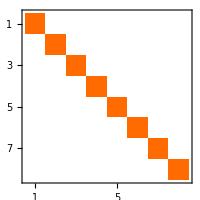
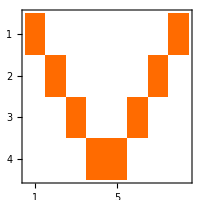
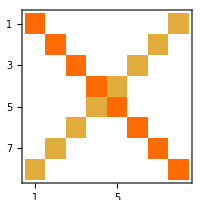
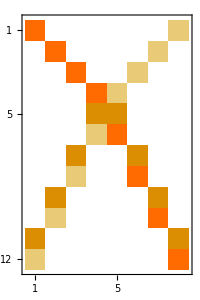
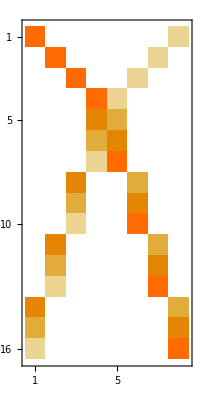
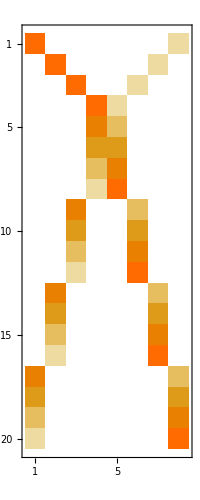
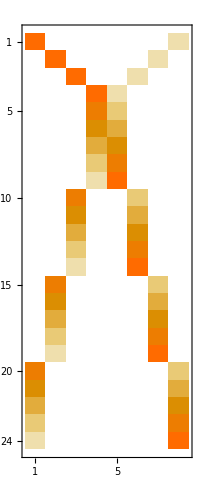
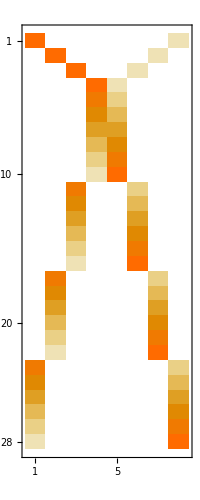
(Height | Weights | Root Vectors | MatrixPlot
1 | ((√5)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2
0 | (√5)/2 | 0 | 0 | 0 | 0 | 1/2 | 0
0 | 0 | (√5)/2 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | (√5)/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | (√5)/2 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | (√5)/2 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | (√5)/2 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | (√5)/2) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1) | -Graphics-
2 | (φ | 0 | 0 | 0 | 0 | 0 | 0 | φ
0 | φ | 0 | 0 | 0 | 0 | φ | 0
0 | 0 | φ | 0 | 0 | φ | 0 | 0
0 | 0 | 0 | φ | φ | 0 | 0 | 0) | (1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0) | -Graphics-
3 | (φ^3/2+1/φ | 0 | 0 | 0 | 0 | 0 | 0 | φ^3/2
0 | φ^3/2+1/φ | 0 | 0 | 0 | 0 | φ^3/2 | 0
0 | 0 | φ^3/2+1/φ | 0 | 0 | φ^3/2 | 0 | 0
0 | 0 | 0 | φ^3/2+1/φ | φ^3/2 | 0 | 0 | 0
0 | 0 | 0 | φ^3/2 | φ^3/2+1/φ | 0 | 0 | 0
0 | 0 | φ^3/2 | 0 | 0 | φ^3/2+1/φ | 0 | 0
0 | φ^3/2 | 0 | 0 | 0 | 0 | φ^3/2+1/φ | 0
φ^3/2 | 0 | 0 | 0 | 0 | 0 | 0 | φ^3/2+1/φ) | (2 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 2 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 2 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 2 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 2 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 2 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 2) | -Graphics-
4 | (3/φ+2 | 0 | 0 | 0 | 0 | 0 | 0 | φ^2
0 | 3/φ+2 | 0 | 0 | 0 | 0 | φ^2 | 0
0 | 0 | 3/φ+2 | 0 | 0 | φ^2 | 0 | 0
0 | 0 | 0 | 3/φ+2 | φ^2 | 0 | 0 | 0
0 | 0 | 0 | 2 φ | 2 φ | 0 | 0 | 0
0 | 0 | 0 | φ^2 | 3/φ+2 | 0 | 0 | 0
0 | 0 | 2 φ | 0 | 0 | 2 φ | 0 | 0
0 | 0 | φ^2 | 0 | 0 | 3/φ+2 | 0 | 0
0 | 2 φ | 0 | 0 | 0 | 0 | 2 φ | 0
0 | φ^2 | 0 | 0 | 0 | 0 | 3/φ+2 | 0
2 φ | 0 | 0 | 0 | 0 | 0 | 0 | 2 φ
φ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 3/φ+2) | (3 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 3 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 3 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 3 | 1 | 0 | 0 | 0
0 | 0 | 0 | 2 | 2 | 0 | 0 | 0
0 | 0 | 0 | 1 | 3 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 2 | 0 | 0
0 | 0 | 1 | 0 | 0 | 3 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 2 | 0
0 | 1 | 0 | 0 | 0 | 0 | 3 | 0
2 | 0 | 0 | 0 | 0 | 0 | 0 | 2
1 | 0 | 0 | 0 | 0 | 0 | 0 | 3) | -Graphics-
5 | (φ^3/2+3/φ+1 | 0 | 0 | 0 | 0 | 0 | 0 | φ^3/2+1
0 | φ^3/2+3/φ+1 | 0 | 0 | 0 | 0 | φ^3/2+1 | 0
0 | 0 | φ^3/2+3/φ+1 | 0 | 0 | φ^3/2+1 | 0 | 0
0 | 0 | 0 | φ^3/2+3/φ+1 | φ^3/2+1 | 0 | 0 | 0
0 | 0 | 0 | φ^3/2+2/φ+1 | 2 φ+1/2 | 0 | 0 | 0
0 | 0 | 0 | 2 φ+1/2 | φ^3/2+2/φ+1 | 0 | 0 | 0
0 | 0 | 0 | φ^3/2+1 | φ^3/2+3/φ+1 | 0 | 0 | 0
0 | 0 | φ^3/2+2/φ+1 | 0 | 0 | 2 φ+1/2 | 0 | 0
0 | 0 | 2 φ+1/2 | 0 | 0 | φ^3/2+2/φ+1 | 0 | 0
0 | 0 | φ^3/2+1 | 0 | 0 | φ^3/2+3/φ+1 | 0 | 0
0 | φ^3/2+2/φ+1 | 0 | 0 | 0 | 0 | 2 φ+1/2 | 0
0 | 2 φ+1/2 | 0 | 0 | 0 | 0 | φ^3/2+2/φ+1 | 0
0 | φ^3/2+1 | 0 | 0 | 0 | 0 | φ^3/2+3/φ+1 | 0
φ^3/2+2/φ+1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 φ+1/2
2 φ+1/2 | 0 | 0 | 0 | 0 | 0 | 0 | φ^3/2+2/φ+1
φ^3/2+1 | 0 | 0 | 0 | 0 | 0 | 0 | φ^3/2+3/φ+1) | (4 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 4 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 4 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 4 | 1 | 0 | 0 | 0
0 | 0 | 0 | 3 | 2 | 0 | 0 | 0
0 | 0 | 0 | 2 | 3 | 0 | 0 | 0
0 | 0 | 0 | 1 | 4 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 2 | 0 | 0
0 | 0 | 2 | 0 | 0 | 3 | 0 | 0
0 | 0 | 1 | 0 | 0 | 4 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0 | 2 | 0
0 | 2 | 0 | 0 | 0 | 0 | 3 | 0
0 | 1 | 0 | 0 | 0 | 0 | 4 | 0
3 | 0 | 0 | 0 | 0 | 0 | 0 | 2
2 | 0 | 0 | 0 | 0 | 0 | 0 | 3
1 | 0 | 0 | 0 | 0 | 0 | 0 | 4) | -Graphics-
6 | (1/2 (φ^3+3)+4/φ | 0 | 0 | 0 | 0 | 0 | 0 | φ+2
0 | 1/2 (φ^3+3)+4/φ | 0 | 0 | 0 | 0 | φ+2 | 0
0 | 0 | 1/2 (φ^3+3)+4/φ | 0 | 0 | φ+2 | 0 | 0
0 | 0 | 0 | 1/2 (φ^3+3)+4/φ | φ+2 | 0 | 0 | 0
0 | 0 | 0 | 1/2 (φ^3+3)+3/φ | φ^3 | 0 | 0 | 0
0 | 0 | 0 | 1/2 (φ^3+3)+2/φ | 1/2 (φ^3+3)+2/φ | 0 | 0 | 0
0 | 0 | 0 | φ^3 | 1/2 (φ^3+3)+3/φ | 0 | 0 | 0
0 | 0 | 0 | φ+2 | 1/2 (φ^3+3)+4/φ | 0 | 0 | 0
0 | 0 | 1/2 (φ^3+3)+3/φ | 0 | 0 | φ^3 | 0 | 0
0 | 0 | 1/2 (φ^3+3)+2/φ | 0 | 0 | 1/2 (φ^3+3)+2/φ | 0 | 0
0 | 0 | φ^3 | 0 | 0 | 1/2 (φ^3+3)+3/φ | 0 | 0
0 | 0 | φ+2 | 0 | 0 | 1/2 (φ^3+3)+4/φ | 0 | 0
0 | 1/2 (φ^3+3)+3/φ | 0 | 0 | 0 | 0 | φ^3 | 0
0 | 1/2 (φ^3+3)+2/φ | 0 | 0 | 0 | 0 | 1/2 (φ^3+3)+2/φ | 0
0 | φ^3 | 0 | 0 | 0 | 0 | 1/2 (φ^3+3)+3/φ | 0
0 | φ+2 | 0 | 0 | 0 | 0 | 1/2 (φ^3+3)+4/φ | 0
1/2 (φ^3+3)+3/φ | 0 | 0 | 0 | 0 | 0 | 0 | φ^3
1/2 (φ^3+3)+2/φ | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (φ^3+3)+2/φ
φ^3 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (φ^3+3)+3/φ
φ+2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (φ^3+3)+4/φ) | (5 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 5 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 5 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 5 | 1 | 0 | 0 | 0
0 | 0 | 0 | 4 | 2 | 0 | 0 | 0
0 | 0 | 0 | 3 | 3 | 0 | 0 | 0
0 | 0 | 0 | 2 | 4 | 0 | 0 | 0
0 | 0 | 0 | 1 | 5 | 0 | 0 | 0
0 | 0 | 4 | 0 | 0 | 2 | 0 | 0
0 | 0 | 3 | 0 | 0 | 3 | 0 | 0
0 | 0 | 2 | 0 | 0 | 4 | 0 | 0
0 | 0 | 1 | 0 | 0 | 5 | 0 | 0
0 | 4 | 0 | 0 | 0 | 0 | 2 | 0
0 | 3 | 0 | 0 | 0 | 0 | 3 | 0
0 | 2 | 0 | 0 | 0 | 0 | 4 | 0
0 | 1 | 0 | 0 | 0 | 0 | 5 | 0
4 | 0 | 0 | 0 | 0 | 0 | 0 | 2
3 | 0 | 0 | 0 | 0 | 0 | 0 | 3
2 | 0 | 0 | 0 | 0 | 0 | 0 | 4
1 | 0 | 0 | 0 | 0 | 0 | 0 | 5) | -Graphics-
7 | (7.2082 | 0 | 0 | 0 | 0 | 0 | 0 | 4.11803
0 | 7.2082 | 0 | 0 | 0 | 0 | 4.11803 | 0
0 | 0 | 7.2082 | 0 | 0 | 4.11803 | 0 | 0
0 | 0 | 0 | 7.2082 | 4.11803 | 0 | 0 | 0
0 | 0 | 0 | 6.59017 | 4.73607 | 0 | 0 | 0
0 | 0 | 0 | 5.97214 | 5.3541 | 0 | 0 | 0
0 | 0 | 0 | 5.3541 | 5.97214 | 0 | 0 | 0
0 | 0 | 0 | 4.73607 | 6.59017 | 0 | 0 | 0
0 | 0 | 0 | 4.11803 | 7.2082 | 0 | 0 | 0
0 | 0 | 6.59017 | 0 | 0 | 4.73607 | 0 | 0
0 | 0 | 5.97214 | 0 | 0 | 5.3541 | 0 | 0
0 | 0 | 5.3541 | 0 | 0 | 5.97214 | 0 | 0
0 | 0 | 4.73607 | 0 | 0 | 6.59017 | 0 | 0
0 | 0 | 4.11803 | 0 | 0 | 7.2082 | 0 | 0
0 | 6.59017 | 0 | 0 | 0 | 0 | 4.73607 | 0
0 | 5.97214 | 0 | 0 | 0 | 0 | 5.3541 | 0
0 | 5.3541 | 0 | 0 | 0 | 0 | 5.97214 | 0
0 | 4.73607 | 0 | 0 | 0 | 0 | 6.59017 | 0
0 | 4.11803 | 0 | 0 | 0 | 0 | 7.2082 | 0
6.59017 | 0 | 0 | 0 | 0 | 0 | 0 | 4.73607
5.97214 | 0 | 0 | 0 | 0 | 0 | 0 | 5.3541
5.3541 | 0 | 0 | 0 | 0 | 0 | 0 | 5.97214
4.73607 | 0 | 0 | 0 | 0 | 0 | 0 | 6.59017
4.11803 | 0 | 0 | 0 | 0 | 0 | 0 | 7.2082) | (6 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 6 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 6 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 6 | 1 | 0 | 0 | 0
0 | 0 | 0 | 5 | 2 | 0 | 0 | 0
0 | 0 | 0 | 4 | 3 | 0 | 0 | 0
0 | 0 | 0 | 3 | 4 | 0 | 0 | 0
0 | 0 | 0 | 2 | 5 | 0 | 0 | 0
0 | 0 | 0 | 1 | 6 | 0 | 0 | 0
0 | 0 | 5 | 0 | 0 | 2 | 0 | 0
0 | 0 | 4 | 0 | 0 | 3 | 0 | 0
0 | 0 | 3 | 0 | 0 | 4 | 0 | 0
0 | 0 | 2 | 0 | 0 | 5 | 0 | 0
0 | 0 | 1 | 0 | 0 | 6 | 0 | 0
0 | 5 | 0 | 0 | 0 | 0 | 2 | 0
0 | 4 | 0 | 0 | 0 | 0 | 3 | 0
0 | 3 | 0 | 0 | 0 | 0 | 4 | 0
0 | 2 | 0 | 0 | 0 | 0 | 5 | 0
0 | 1 | 0 | 0 | 0 | 0 | 6 | 0
5 | 0 | 0 | 0 | 0 | 0 | 0 | 2
4 | 0 | 0 | 0 | 0 | 0 | 0 | 3
3 | 0 | 0 | 0 | 0 | 0 | 0 | 4
2 | 0 | 0 | 0 | 0 | 0 | 0 | 5
1 | 0 | 0 | 0 | 0 | 0 | 0 | 6) | -Graphics-
8 | (8.32624 | 0 | 0 | 0 | 0 | 0 | 0 | φ+3
0 | 8.32624 | 0 | 0 | 0 | 0 | φ+3 | 0
0 | 0 | 8.32624 | 0 | 0 | φ+3 | 0 | 0
0 | 0 | 0 | 8.32624 | φ+3 | 0 | 0 | 0
0 | 0 | 0 | 7.7082 | 2 φ^2 | 0 | 0 | 0
0 | 0 | 0 | 7.09017 | 5.8541 | 0 | 0 | 0
0 | 0 | 0 | 6.47214 | 6.47214 | 0 | 0 | 0
0 | 0 | 0 | 5.8541 | 7.09017 | 0 | 0 | 0
0 | 0 | 0 | 2 φ^2 | 7.7082 | 0 | 0 | 0
0 | 0 | 0 | φ+3 | 8.32624 | 0 | 0 | 0
0 | 0 | 7.7082 | 0 | 0 | 2 φ^2 | 0 | 0
0 | 0 | 7.09017 | 0 | 0 | 5.8541 | 0 | 0
0 | 0 | 6.47214 | 0 | 0 | 6.47214 | 0 | 0
0 | 0 | 5.8541 | 0 | 0 | 7.09017 | 0 | 0
0 | 0 | 2 φ^2 | 0 | 0 | 7.7082 | 0 | 0
0 | 0 | φ+3 | 0 | 0 | 8.32624 | 0 | 0
0 | 7.7082 | 0 | 0 | 0 | 0 | 2 φ^2 | 0
0 | 7.09017 | 0 | 0 | 0 | 0 | 5.8541 | 0
0 | 6.47214 | 0 | 0 | 0 | 0 | 6.47214 | 0
0 | 5.8541 | 0 | 0 | 0 | 0 | 7.09017 | 0
0 | 2 φ^2 | 0 | 0 | 0 | 0 | 7.7082 | 0
0 | φ+3 | 0 | 0 | 0 | 0 | 8.32624 | 0
7.7082 | 0 | 0 | 0 | 0 | 0 | 0 | 2 φ^2
7.09017 | 0 | 0 | 0 | 0 | 0 | 0 | 5.8541
6.47214 | 0 | 0 | 0 | 0 | 0 | 0 | 6.47214
5.8541 | 0 | 0 | 0 | 0 | 0 | 0 | 7.09017
2 φ^2 | 0 | 0 | 0 | 0 | 0 | 0 | 7.7082
φ+3 | 0 | 0 | 0 | 0 | 0 | 0 | 8.32624) | (7 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 7 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 7 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 7 | 1 | 0 | 0 | 0
0 | 0 | 0 | 6 | 2 | 0 | 0 | 0
0 | 0 | 0 | 5 | 3 | 0 | 0 | 0
0 | 0 | 0 | 4 | 4 | 0 | 0 | 0
0 | 0 | 0 | 3 | 5 | 0 | 0 | 0
0 | 0 | 0 | 2 | 6 | 0 | 0 | 0
0 | 0 | 0 | 1 | 7 | 0 | 0 | 0
0 | 0 | 6 | 0 | 0 | 2 | 0 | 0
0 | 0 | 5 | 0 | 0 | 3 | 0 | 0
0 | 0 | 4 | 0 | 0 | 4 | 0 | 0
0 | 0 | 3 | 0 | 0 | 5 | 0 | 0
0 | 0 | 2 | 0 | 0 | 6 | 0 | 0
0 | 0 | 1 | 0 | 0 | 7 | 0 | 0
0 | 6 | 0 | 0 | 0 | 0 | 2 | 0
0 | 5 | 0 | 0 | 0 | 0 | 3 | 0
0 | 4 | 0 | 0 | 0 | 0 | 4 | 0
0 | 3 | 0 | 0 | 0 | 0 | 5 | 0
0 | 2 | 0 | 0 | 0 | 0 | 6 | 0
0 | 1 | 0 | 0 | 0 | 0 | 7 | 0
6 | 0 | 0 | 0 | 0 | 0 | 0 | 2
5 | 0 | 0 | 0 | 0 | 0 | 0 | 3
4 | 0 | 0 | 0 | 0 | 0 | 0 | 4
3 | 0 | 0 | 0 | 0 | 0 | 0 | 5
2 | 0 | 0 | 0 | 0 | 0 | 0 | 6
1 | 0 | 0 | 0 | 0 | 0 | 0 | 7) | -Graphics-
9 | (9.44427 | 0 | 0 | 0 | 0 | 0 | 0 | 5.11803
0 | 9.44427 | 0 | 0 | 0 | 0 | 5.11803 | 0
0 | 0 | 9.44427 | 0 | 0 | 5.11803 | 0 | 0
0 | 0 | 0 | 9.44427 | 5.11803 | 0 | 0 | 0
0 | 0 | 0 | 8.82624 | 5.73607 | 0 | 0 | 0
0 | 0 | 0 | 8.2082 | 6.3541 | 0 | 0 | 0
0 | 0 | 0 | 7.59017 | 6.97214 | 0 | 0 | 0
0 | 0 | 0 | 6.97214 | 7.59017 | 0 | 0 | 0
0 | 0 | 0 | 6.3541 | 8.2082 | 0 | 0 | 0
0 | 0 | 0 | 5.73607 | 8.82624 | 0 | 0 | 0
0 | 0 | 0 | 5.11803 | 9.44427 | 0 | 0 | 0
0 | 0 | 8.82624 | 0 | 0 | 5.73607 | 0 | 0
0 | 0 | 8.2082 | 0 | 0 | 6.3541 | 0 | 0
0 | 0 | 7.59017 | 0 | 0 | 6.97214 | 0 | 0
0 | 0 | 6.97214 | 0 | 0 | 7.59017 | 0 | 0
0 | 0 | 6.3541 | 0 | 0 | 8.2082 | 0 | 0
0 | 0 | 5.73607 | 0 | 0 | 8.82624 | 0 | 0
0 | 0 | 5.11803 | 0 | 0 | 9.44427 | 0 | 0
0 | 8.82624 | 0 | 0 | 0 | 0 | 5.73607 | 0
0 | 8.2082 | 0 | 0 | 0 | 0 | 6.3541 | 0
0 | 7.59017 | 0 | 0 | 0 | 0 | 6.97214 | 0
0 | 6.97214 | 0 | 0 | 0 | 0 | 7.59017 | 0
0 | 6.3541 | 0 | 0 | 0 | 0 | 8.2082 | 0
0 | 5.73607 | 0 | 0 | 0 | 0 | 8.82624 | 0
0 | 5.11803 | 0 | 0 | 0 | 0 | 9.44427 | 0
8.82624 | 0 | 0 | 0 | 0 | 0 | 0 | 5.73607
8.2082 | 0 | 0 | 0 | 0 | 0 | 0 | 6.3541
7.59017 | 0 | 0 | 0 | 0 | 0 | 0 | 6.97214
6.97214 | 0 | 0 | 0 | 0 | 0 | 0 | 7.59017
6.3541 | 0 | 0 | 0 | 0 | 0 | 0 | 8.2082
5.73607 | 0 | 0 | 0 | 0 | 0 | 0 | 8.82624
5.11803 | 0 | 0 | 0 | 0 | 0 | 0 | 9.44427) | (8 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 8 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 8 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 8 | 1 | 0 | 0 | 0
0 | 0 | 0 | 7 | 2 | 0 | 0 | 0
0 | 0 | 0 | 6 | 3 | 0 | 0 | 0
0 | 0 | 0 | 5 | 4 | 0 | 0 | 0
0 | 0 | 0 | 4 | 5 | 0 | 0 | 0
0 | 0 | 0 | 3 | 6 | 0 | 0 | 0
0 | 0 | 0 | 2 | 7 | 0 | 0 | 0
0 | 0 | 0 | 1 | 8 | 0 | 0 | 0
0 | 0 | 7 | 0 | 0 | 2 | 0 | 0
0 | 0 | 6 | 0 | 0 | 3 | 0 | 0
0 | 0 | 5 | 0 | 0 | 4 | 0 | 0
0 | 0 | 4 | 0 | 0 | 5 | 0 | 0
0 | 0 | 3 | 0 | 0 | 6 | 0 | 0
0 | 0 | 2 | 0 | 0 | 7 | 0 | 0
0 | 0 | 1 | 0 | 0 | 8 | 0 | 0
0 | 7 | 0 | 0 | 0 | 0 | 2 | 0
0 | 6 | 0 | 0 | 0 | 0 | 3 | 0
0 | 5 | 0 | 0 | 0 | 0 | 4 | 0
0 | 4 | 0 | 0 | 0 | 0 | 5 | 0
0 | 3 | 0 | 0 | 0 | 0 | 6 | 0
0 | 2 | 0 | 0 | 0 | 0 | 7 | 0
0 | 1 | 0 | 0 | 0 | 0 | 8 | 0
7 | 0 | 0 | 0 | 0 | 0 | 0 | 2
6 | 0 | 0 | 0 | 0 | 0 | 0 | 3
5 | 0 | 0 | 0 | 0 | 0 | 0 | 4
4 | 0 | 0 | 0 | 0 | 0 | 0 | 5
3 | 0 | 0 | 0 | 0 | 0 | 0 | 6
2 | 0 | 0 | 0 | 0 | 0 | 0 | 7
1 | 0 | 0 | 0 | 0 | 0 | 0 | 8) | -Graphics-
10 | (10.5623 | 0 | 0 | 0 | 0 | 0 | 0 | 5.61803
0 | 10.5623 | 0 | 0 | 0 | 0 | 5.61803 | 0
0 | 0 | 10.5623 | 0 | 0 | 5.61803 | 0 | 0
0 | 0 | 0 | 10.5623 | 5.61803 | 0 | 0 | 0
0 | 0 | 0 | 9.94427 | 6.23607 | 0 | 0 | 0
0 | 0 | 0 | 9.32624 | 6.8541 | 0 | 0 | 0
0 | 0 | 0 | 8.7082 | 7.47214 | 0 | 0 | 0
0 | 0 | 0 | 8.09017 | 8.09017 | 0 | 0 | 0
0 | 0 | 0 | 7.47214 | 8.7082 | 0 | 0 | 0
0 | 0 | 0 | 6.8541 | 9.32624 | 0 | 0 | 0
0 | 0 | 0 | 6.23607 | 9.94427 | 0 | 0 | 0
0 | 0 | 0 | 5.61803 | 10.5623 | 0 | 0 | 0
0 | 0 | 9.94427 | 0 | 0 | 6.23607 | 0 | 0
0 | 0 | 9.32624 | 0 | 0 | 6.8541 | 0 | 0
0 | 0 | 8.7082 | 0 | 0 | 7.47214 | 0 | 0
0 | 0 | 8.09017 | 0 | 0 | 8.09017 | 0 | 0
0 | 0 | 7.47214 | 0 | 0 | 8.7082 | 0 | 0
0 | 0 | 6.8541 | 0 | 0 | 9.32624 | 0 | 0
0 | 0 | 6.23607 | 0 | 0 | 9.94427 | 0 | 0
0 | 0 | 5.61803 | 0 | 0 | 10.5623 | 0 | 0
0 | 9.94427 | 0 | 0 | 0 | 0 | 6.23607 | 0
0 | 9.32624 | 0 | 0 | 0 | 0 | 6.8541 | 0
0 | 8.7082 | 0 | 0 | 0 | 0 | 7.47214 | 0
0 | 8.09017 | 0 | 0 | 0 | 0 | 8.09017 | 0
0 | 7.47214 | 0 | 0 | 0 | 0 | 8.7082 | 0
0 | 6.8541 | 0 | 0 | 0 | 0 | 9.32624 | 0
0 | 6.23607 | 0 | 0 | 0 | 0 | 9.94427 | 0
0 | 5.61803 | 0 | 0 | 0 | 0 | 10.5623 | 0
9.94427 | 0 | 0 | 0 | 0 | 0 | 0 | 6.23607
9.32624 | 0 | 0 | 0 | 0 | 0 | 0 | 6.8541
8.7082 | 0 | 0 | 0 | 0 | 0 | 0 | 7.47214
8.09017 | 0 | 0 | 0 | 0 | 0 | 0 | 8.09017
7.47214 | 0 | 0 | 0 | 0 | 0 | 0 | 8.7082
6.8541 | 0 | 0 | 0 | 0 | 0 | 0 | 9.32624
6.23607 | 0 | 0 | 0 | 0 | 0 | 0 | 9.94427
5.61803 | 0 | 0 | 0 | 0 | 0 | 0 | 10.5623) | (9 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 9 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 9 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 9 | 1 | 0 | 0 | 0
0 | 0 | 0 | 8 | 2 | 0 | 0 | 0
0 | 0 | 0 | 7 | 3 | 0 | 0 | 0
0 | 0 | 0 | 6 | 4 | 0 | 0 | 0
0 | 0 | 0 | 5 | 5 | 0 | 0 | 0
0 | 0 | 0 | 4 | 6 | 0 | 0 | 0
0 | 0 | 0 | 3 | 7 | 0 | 0 | 0
0 | 0 | 0 | 2 | 8 | 0 | 0 | 0
0 | 0 | 0 | 1 | 9 | 0 | 0 | 0
0 | 0 | 8 | 0 | 0 | 2 | 0 | 0
0 | 0 | 7 | 0 | 0 | 3 | 0 | 0
0 | 0 | 6 | 0 | 0 | 4 | 0 | 0
0 | 0 | 5 | 0 | 0 | 5 | 0 | 0
0 | 0 | 4 | 0 | 0 | 6 | 0 | 0
0 | 0 | 3 | 0 | 0 | 7 | 0 | 0
0 | 0 | 2 | 0 | 0 | 8 | 0 | 0
0 | 0 | 1 | 0 | 0 | 9 | 0 | 0
0 | 8 | 0 | 0 | 0 | 0 | 2 | 0
0 | 7 | 0 | 0 | 0 | 0 | 3 | 0
0 | 6 | 0 | 0 | 0 | 0 | 4 | 0
0 | 5 | 0 | 0 | 0 | 0 | 5 | 0
0 | 4 | 0 | 0 | 0 | 0 | 6 | 0
0 | 3 | 0 | 0 | 0 | 0 | 7 | 0
0 | 2 | 0 | 0 | 0 | 0 | 8 | 0
0 | 1 | 0 | 0 | 0 | 0 | 9 | 0
8 | 0 | 0 | 0 | 0 | 0 | 0 | 2
7 | 0 | 0 | 0 | 0 | 0 | 0 | 3
6 | 0 | 0 | 0 | 0 | 0 | 0 | 4
5 | 0 | 0 | 0 | 0 | 0 | 0 | 5
4 | 0 | 0 | 0 | 0 | 0 | 0 | 6
3 | 0 | 0 | 0 | 0 | 0 | 0 | 7
2 | 0 | 0 | 0 | 0 | 0 | 0 | 8
1 | 0 | 0 | 0 | 0 | 0 | 0 | 9) | -Graphics-)

```mathematica
rootHeights=rootVecs⟦#⟦1⟧;;#⟦2⟧⟧&/@indices;
weightHeights=weightsSym⟦#⟦1⟧;;#⟦2⟧⟧&/@indices;
Join[{{"Height","Weights","Root Vectors","MatrixPlot"}},
{#,weightHeights⟦#⟧,rootHeights⟦#⟧,MatrixPlot[rootHeights⟦#⟧,ImageSize->200]}&/@Range@Length@indices]
```

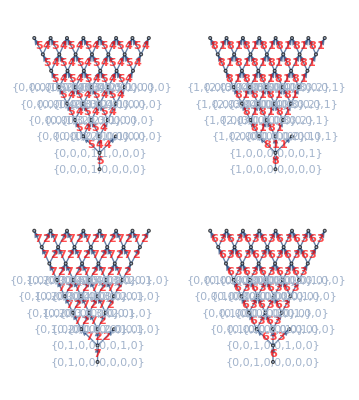

```mathematica
doHasse
```

Fig. 5 Analysis of cm𝕌-cm𝕌^-1 showing all integer positive roots, weights, heights

```mathematica
Import@"revIMroots.svg"
```

-Graphics-

Fig. 6 Analysis of cm𝕌-cm𝕌^-1 showing its Hasse visualizations up to height 10, which are identical to those in Fig. 4

```mathematica
Import@"revIMHasse.svg"
```

-Graphics-

## Appendix B:

Orthogonal projection to 3D of the cm𝕌-based vertex coordinates using dimensions {2,3,4}.

These were created using quaternion Weyl orbits directly from the A_3, B_3,and H_3 group symmetries[4] listed in the first column.

Fig. 7 Orthogonal projection to 3D of the cm𝕌-based vertex coordinates using dimensions {2,3,4}, noting the regular octahedral and irregular icosahedral hulls}

Dims used={2, 3, 4} 
tallyList={60,12,6,12}
{6,12,12,12}
{6,12,12,12}
{12,12,6,12}
{12,12}
(Hull # = 2
with 12 vertices
of 3D Norm | = | 1/2 √(φ+1/φ)
 | = | 0.747674
 | = | 0.74767
Vertex #'s = {61,72})
-Graphics3D- | (Hull # = 3
with 6 vertices
of 3D Norm | = | √φ
 | = | 1.27202
 | = | 1.27202
Vertex #'s = {73,78})
-Graphics3D- | (Hull # = 4
with 12 vertices
of 3D Norm | = | 1/2 √(9 φ+1/φ)
 | = | 1.9481
 | = | 1.9481
Vertex #'s = {79,90})
-Graphics3D- | (Hull # = 5
with 6 vertices
of 3D Norm | = | 2 √φ
 | = | 2.54404
 | = | 2.54404
Vertex #'s = {91,96})
-Graphics3D-
(Hull # = 6
with 12 vertices
of 3D Norm | = | √(4 φ+1/φ)
 | = | 2.66274
 | = | 2.66274
Vertex #'s = {97,108})
-Graphics3D- | (Hull # = 7
with 12 vertices
of 3D Norm | = | 1/2 √(25 φ+1/φ)
 | = | 3.20425
 | = | 3.20425
Vertex #'s = {109,120})
-Graphics3D- | (Hull # = 8
with 12 vertices
of 3D Norm | = | √((25 φ)/4+9/(4 φ))
 | = | 3.39165
 | = | 3.39165
Vertex #'s = {121,132})
-Graphics3D- | (Hull # = 9
with 6 vertices
of 3D Norm | = | 3 √φ
 | = | 3.81606
 | = | 3.81606
Vertex #'s = {133,138})
-Graphics3D-
(Hull # = 10
with 12 vertices
of 3D Norm | = | √(9 φ+1/φ)
 | = | 3.8962
 | = | 3.8962
Vertex #'s = {139,150})
-Graphics3D- | (Hull # = 11
with 12 vertices
of 3D Norm | = | √(9 φ+4/φ)
 | = | 4.12728
 | = | 4.12728
Vertex #'s = {151,162})
-Graphics3D- | (Hull # = 12
with 12 vertices
of 3D Norm | = | 1/2 √(49 φ+1/φ)
 | = | 4.46939
 | = | 4.46939
Vertex #'s = {163,174})
-Graphics3D- | (Hull # = 13
with 12 vertices
of 3D Norm | = | √((49 φ)/4+9/(4 φ))
 | = | 4.60559
 | = | 4.60559
Vertex #'s = {175,186})
-Graphics3D-
(Hull # = 14
with 12 vertices
of 3D Norm | = | √((49 φ)/4+25/(4 φ))
 | = | 4.86658
 | = | 4.86658
Vertex #'s = {187,198})
-Graphics3D- | (Hull # = 15
with 6 vertices
of 3D Norm | = | 4 √φ
 | = | 5.08808
 | = | 5.08808
Vertex #'s = {199,204})
-Graphics3D- | (Hull # = 16
with 12 vertices
of 3D Norm | = | √(16 φ+1/φ)
 | = | 5.14845
 | = | 5.14845
Vertex #'s = {205,216})
-Graphics3D- | (Hull # = 17
with 12 vertices
of 3D Norm | = | √(16 φ+4/φ)
 | = | 5.32547
 | = | 5.32547
Vertex #'s = {217,228})
-Graphics3D-
(Hull # = 18
with 12 vertices
of 3D Norm | = | √(16 φ+9/φ)
 | = | 5.60811
 | = | 5.60811
Vertex #'s = {229,240})
-Graphics3D- | Combined Hulls=
-Graphics3D-
Overall Hull=
-Graphics3D- |  |